# Setup

```mathematica
(* ================================================================ *)
(* MODULE 0: SETUP                                                  *)
(* ================================================================ *)

baseDir = NotebookDirectory[];
Get[FileNameJoin[{baseDir, "QKT_full.wl"}]];
$HistoryLength = 0;
EnsureDir[dir_] := If[!DirectoryQ[dir],
  CreateDirectory[dir, CreateIntermediateDirectories -> True]];
kStr[k_] := StringReplace[
  If[StringEndsQ[#, "."], # <> "0", #] &[ToString[N[k]]], "." -> "_"];
```

```mathematica
LaunchKernels[14];
```

# QKT functions used

The definition of the sym and non-sym are in the .wl file

```mathematica
Clear[GetQKTParityEigensystem];
GetQKTParityEigensystem[jParam_, alphaParam_, kParam_] :=
  Module[{d=2 jParam + 1,mat, idx, matEven, matOdd, esEven, esOdd,phEven, phOdd, vecsEven, vecsOdd, idxE, idxO,fullVecsEven, fullVecsOdd},
  
(*1. Non symmetric Floquet operator in Jz basis*)
(*mat = Floq[jParam, alphaParam, kParam];*)

(*2. Symmetric Floquet operator in Jz basis*)
mat = Floqsym[jParam, alphaParam, kParam];


    idx = ParitySectorIndices[jParam];
    matEven = mat[[idx["Even"], idx["Even"]]];
    matOdd  = mat[[idx["Odd"], idx["Odd"]]];
    esEven = Eigensystem[matEven, Method -> "Direct"];
    esOdd  = Eigensystem[matOdd, Method -> "Direct"];
    phEven = Mod[Arg[esEven[[1]]], 2 Pi];
    phOdd  = Mod[Arg[esOdd[[1]]], 2 Pi];

    idxE = Ordering[phEven];
idxO = Ordering[phOdd];
    vecsEven = esEven[[2, idxE]];
    vecsOdd  = esOdd[[2, idxO]];
    fullVecsEven = Table[
      Module[{vec = ConstantArray[0. + 0. I, d]},
        vec[[idx["Even"]]] = vecsEven[[i]]; vec],
      {i, Length[idx["Even"]]}];

    fullVecsOdd = Table[
      Module[{vec = ConstantArray[0. + 0. I, d]},
        vec[[idx["Odd"]]] = vecsOdd[[i]]; vec],
      {i, Length[idx["Odd"]]}];

    <|"Even" -> <|"Quasienergies" -> esEven[[1]],
                  "Phases" -> phEven,
                  "Vectors" -> vecsEven,
                  "FullVectors" -> fullVecsEven|>,
      "Odd"  -> <|"Quasienergies" -> esOdd[[1]], 
                  "Phases" -> phOdd,
                  "Vectors" -> vecsOdd,
                  "FullVectors" -> fullVecsOdd|>|>
  ]
```

# Texture

```mathematica
(* ============================================================ *)
(* ENSEMBLE TEXTURE FUNCTION                                     *)
(* ============================================================ *)
Clear[EnsembleTexFull];
EnsembleTexFull[ensembleList_List, tMax_Integer] :=
  Module[{nMat = Length[ensembleList], tGrid = Range[0, tMax],
          allFull, allDiag, allOffDiag},
    Print["Processing ", nMat, " realizations up to t = ", tMax, "..."];
    DistributeDefinitions[tGrid];
    {allFull, allDiag} = Transpose@ParallelTable[
      Module[{phases, vecs, d, f1, pArray, diagPart, fullTex},
        phases   = ensembleList[[i, "Phases"]];
        vecs     = ensembleList[[i, "Vectors"]];
        d        = Length[phases];
        f1       = N@ConstantArray[1/Sqrt[d], d];
        pArray   = Abs[Conjugate[vecs] . f1]^2;
        diagPart = d * Total[pArray^2];
        fullTex  = Table[d * Abs[Total[pArray * Exp[-I t phases]]]^2, {t, tGrid}];
        {fullTex, ConstantArray[diagPart, Length[tGrid]]}
      ], {i, nMat}, Method -> "CoarsestGrained"];
    allOffDiag = allFull - allDiag;
    <|"Time"       -> tGrid,
      "AllTex"     -> allFull,     (* backward compat *)
      "AllFull"    -> allFull,     "MeanFull"    -> Mean[allFull],
      "AllDiag"    -> allDiag,     "MeanDiag"    -> Mean[allDiag],
      "AllOffDiag" -> allOffDiag,  "MeanOffDiag" -> Mean[allOffDiag]|>];
```

```mathematica
(* ============================================================ *)
(* PARAMETERS + ENSEMBLE GENERATION                             *)
(* ============================================================ *)
nQKT    = 500;
J       = 50;
α       = 0.84;
kCenter = 10.5;
δ       = 0.01;
kList   = RandomReal[{kCenter - δ, kCenter + δ}, nQKT];

Print["Generating ", nQKT, " matrices..."];
rawEnsembleData = ParallelTable[
  GetQKTParityEigensystem[J, α, k], {k, kList},
  Method -> "CoarsestGrained"];

qktEnsemble = <|
  "Even" -> Table[<|"Phases"  -> Arg[data["Even", "Quasienergies"]],
                    "Vectors" -> data["Even", "Vectors"]|>, {data, rawEnsembleData}],
  "Odd"  -> Table[<|"Phases"  -> Arg[data["Odd",  "Quasienergies"]],
                    "Vectors" -> data["Odd",  "Vectors"]|>, {data, rawEnsembleData}]|>;
```

Generating 500 matrices...

```mathematica
(* ============================================================ *)
(* COMPUTE TEXTURE                                               *)
(* ============================================================ *)
tMaxTex = 10000;
sigmaSm = 10;

Print["Computing Even Sector..."];
texEven = EnsembleTexFull[qktEnsemble["Even"], tMaxTex];
Print["Computing Odd Sector..."];
texOdd  = EnsembleTexFull[qktEnsemble["Odd"],  tMaxTex];

tGrid = texEven["Time"];

(* SMOOTH *)
texEvenAllSm  = Map[GaussianFilter[#, sigmaSm] &, texEven["AllFull"]];
texOddAllSm   = Map[GaussianFilter[#, sigmaSm] &, texOdd["AllFull"]];
texEvenMeanSm = Mean[texEvenAllSm];
texOddMeanSm  = Mean[texOddAllSm];
```

Computing Even Sector...

Processing 500 realizations up to t = 10000...

Computing Odd Sector...

Processing 500 realizations up to t = 10000...

```mathematica
(* Diagonal and off-diagonal smoothed means *)
texEvenDiagSm   = Mean[Map[GaussianFilter[#, sigmaSm] &, texEven["AllDiag"]]];
texOddDiagSm    = Mean[Map[GaussianFilter[#, sigmaSm] &, texOdd["AllDiag"]]];
texEvenOffDSm   = Mean[Map[GaussianFilter[#, sigmaSm] &, texEven["AllOffDiag"]]];
texOddOffDSm    = Mean[Map[GaussianFilter[#, sigmaSm] &, texOdd["AllOffDiag"]]];
```

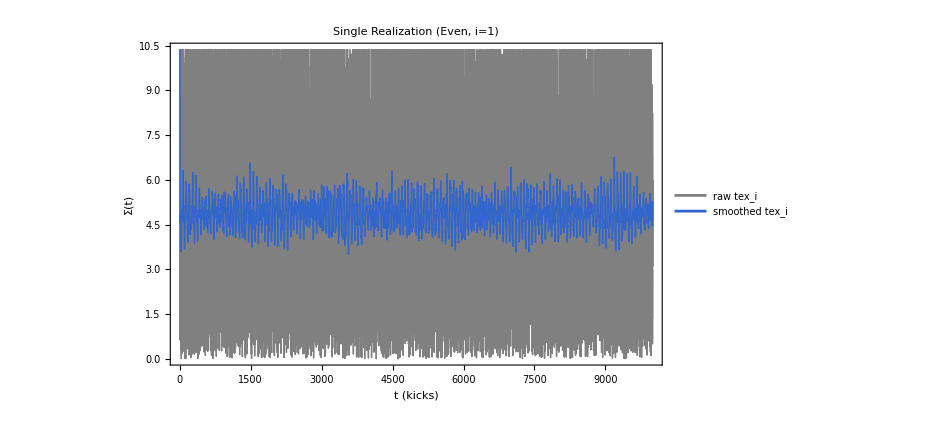

```mathematica
(* ============================================================ *)
(* PLOT 1: Single realization                                    *)
(* ============================================================ *)
iShow = 1;
plotIndivTex = ListLinePlot[
  {Transpose[{tGrid, texEven["AllTex"][[iShow]]}],
   Transpose[{tGrid, texEvenAllSm[[iShow]]}]},
  PlotStyle   -> {Directive[Thin, Gray], Directive[Thick, RGBColor[0.2, 0.4, 0.8]]},
  PlotLegends -> {"raw tex_i", "smoothed tex_i"},
  Frame -> True, FrameLabel -> {"t (kicks)", "Σ(t)"},
  PlotLabel -> "Single Realization (Even, i=" <> ToString[iShow] <> ")",
  ImageSize -> 700, LabelStyle -> Directive[Black, 16]]
```

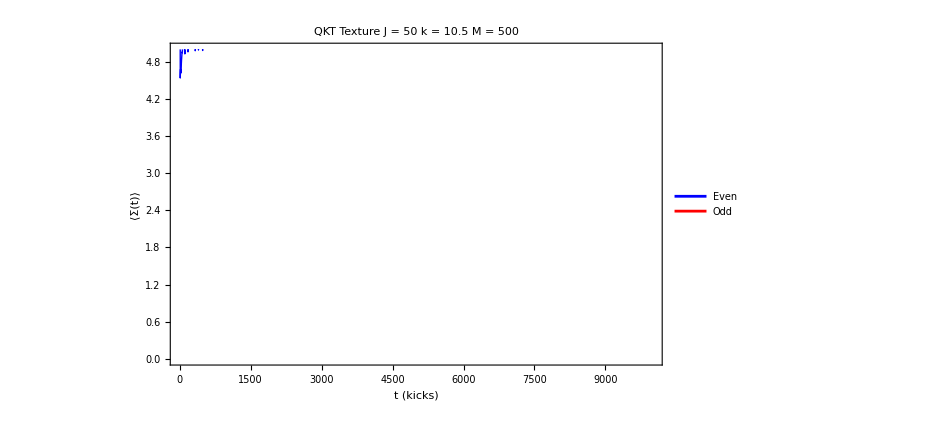

```mathematica
(* ============================================================ *)
(* PLOT 2: Ensemble mean full                                    *)
(* ============================================================ *)
plotMeanTex = ListLinePlot[
  {Transpose[{tGrid, texEvenMeanSm}],
   Transpose[{tGrid, texOddMeanSm}]},
  PlotStyle   -> {Directive[Thick, Blue], Directive[Thick, Red]},
  PlotLegends -> {"Even", "Odd"},
  Frame -> True, FrameLabel -> {"t (kicks)", "⟨Σ(t)⟩"},
  PlotLabel -> "QKT Texture  J = " <> ToString[J] <>
               "  k = " <> ToString[kCenter] <>
               "  M = " <> ToString[nQKT],
  ImageSize -> 700, LabelStyle -> Directive[Black, 16],
  PlotRange -> {All, {0,5}}]
```

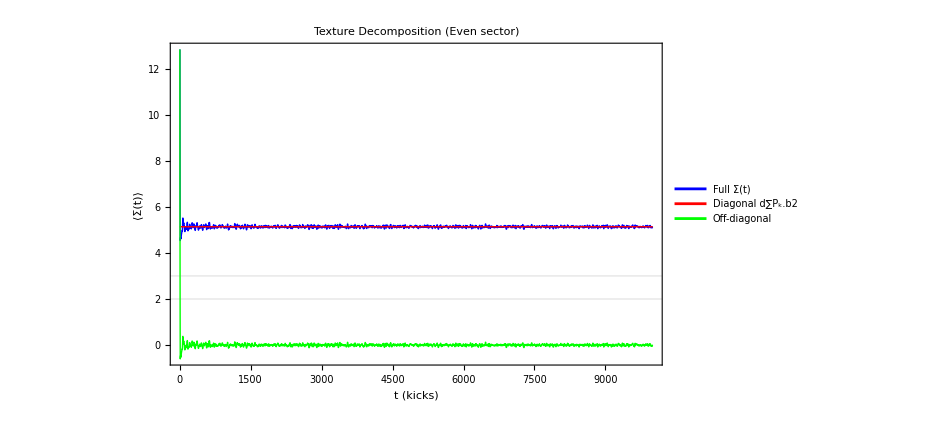

```mathematica
(* ============================================================ *)
(* PLOT 3: Diagonal vs off-diagonal vs full (even sector)       *)
(* ============================================================ *)
plotDecomp = ListLinePlot[
  {Transpose[{tGrid, texEvenMeanSm}],
   Transpose[{tGrid, texEvenDiagSm}],
   Transpose[{tGrid, texEvenOffDSm}]},
  PlotStyle   -> {Directive[Thick, Blue],
                  Directive[Thick, Red],
                  Directive[Thick, Green]},
  PlotLegends -> {"Full Σ(t)", "Diagonal d∑Pₖ.b2", "Off-diagonal"},
  Frame -> True, FrameLabel -> {"t (kicks)", "⟨Σ(t)⟩"},
  PlotLabel -> "Texture Decomposition (Even sector)",
  GridLines -> {None, {2, 3}},
  ImageSize -> 700, LabelStyle -> Directive[Black, 16]]
```

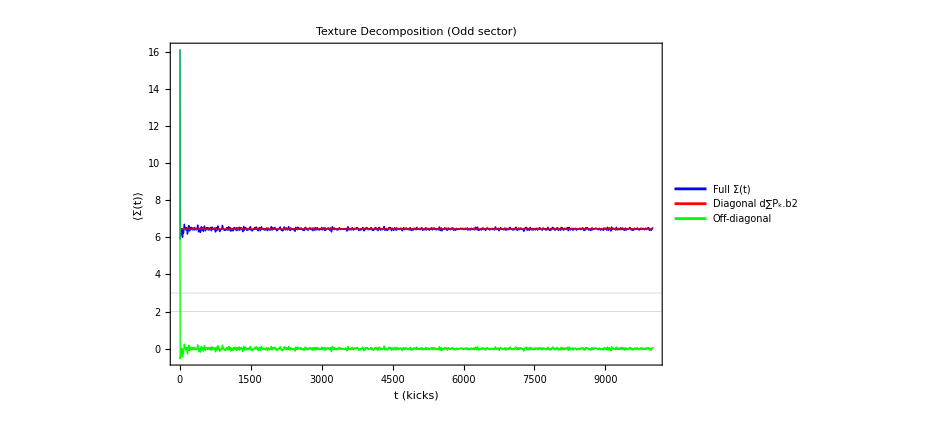

```mathematica
plotDecomp = ListLinePlot[
  {Transpose[{tGrid, texOddMeanSm}],
   Transpose[{tGrid, texOddDiagSm}],
   Transpose[{tGrid, texOddOffDSm}]},
  PlotStyle   -> {Directive[Thick, Blue],
                  Directive[Thick, Red],
                  Directive[Thick, Green]},
  PlotLegends -> {"Full Σ(t)", "Diagonal d∑Pₖ.b2", "Off-diagonal"},
  Frame -> True, FrameLabel -> {"t (kicks)", "⟨Σ(t)⟩"},
  PlotLabel -> "Texture Decomposition (Odd sector)",
  GridLines -> {None, {2, 3}},
  ImageSize -> 700, LabelStyle -> Directive[Black, 16]]
```

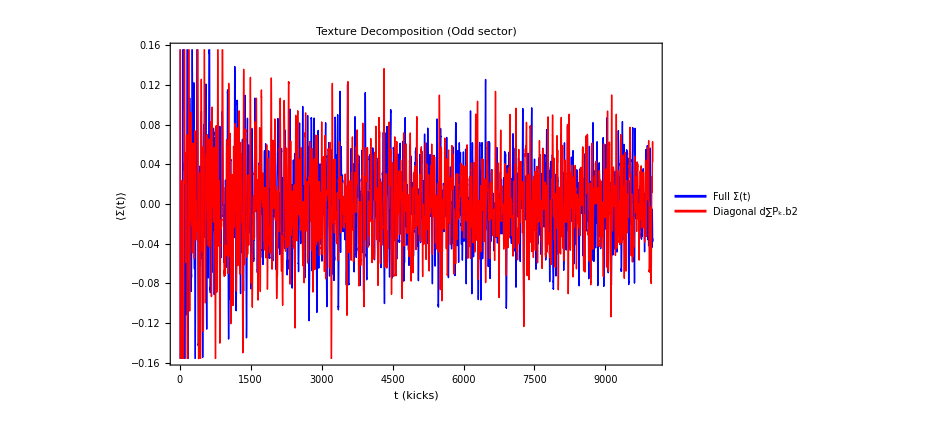

```mathematica
ListLinePlot[
  {Transpose[{tGrid, texEvenOffDSm}],
   Transpose[{tGrid, texOddOffDSm}]},
  PlotStyle   -> {Directive[Thick, Blue],
                  Directive[Thick, Red],
                  Directive[Thick, Green]},
  PlotLegends -> {"Full Σ(t)", "Diagonal d∑Pₖ.b2", "Off-diagonal"},
  Frame -> True, FrameLabel -> {"t (kicks)", "⟨Σ(t)⟩"},
  PlotLabel -> "Texture Decomposition (Odd sector)",
  GridLines -> {None, {2, 3}},
  ImageSize -> 700, LabelStyle -> Directive[Black, 16]]
```